```mathematica
mNum=100
m=Range[mNum];
```

100

```mathematica
Table[{RandomChoice[m], RandomChoice[m]}, 10]
```

{{86,93},{26,82},{84,96},{46,40},{82,19},{25,68},{22,64},{70,69},{24,61},{34,73}}

```mathematica
data = Import["/Users/oogasawa/works/Kauffmans-smulation/result.100.out", Table]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
data10= Import["/Users/oogasawa/works/Kauffmans-simulation/result.10.out", "Table"];
```

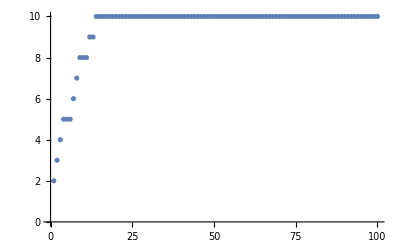

```mathematica
ListPlot[data10[[All,3]]]
```

```mathematica
data100 = Import["/Users/oogasawa/works/Kauffmans-simulation/result.100.out", "Table"];
```

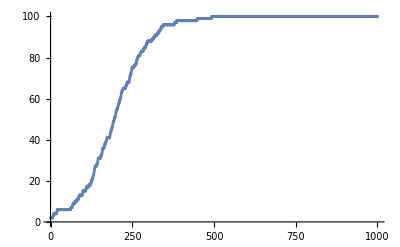

```mathematica
ListPlot[data100[[All, 3]]]
```

```mathematica
data = Import["/Users/oogasawa/works/Kauffmans-simulation/result.1000.out", "Table"];
```

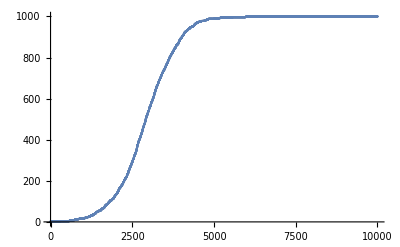

```mathematica
ListPlot[data[[All, 3]]]
```

```mathematica
data4 = Import["/Users/oogasawa/works/Kauffmans-simulation/result.10000.out", "Table"];
```

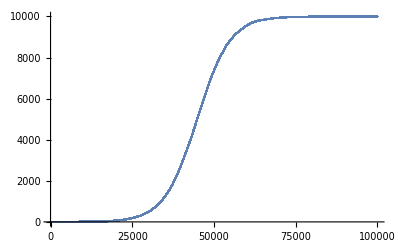

```mathematica
ListPlot[data4[[All,3]]]
```

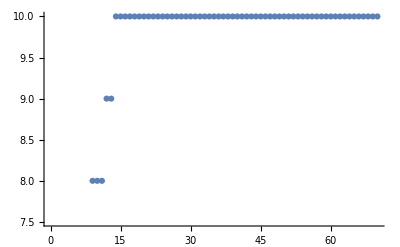

```mathematica
ListPlot[Take[data10[[All,3]],70]]
```

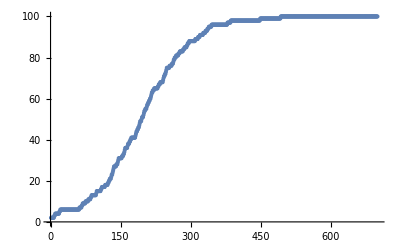

```mathematica
ListPlot[Take[data100[[All,3]],700]]
```

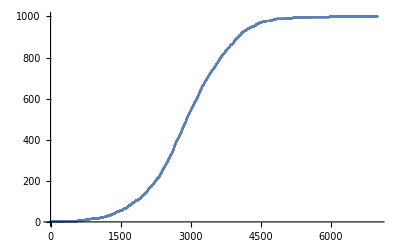

```mathematica
ListPlot[Take[data[[All,3]],7000]]
```

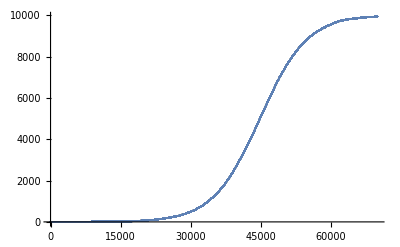

```mathematica
ListPlot[Take[data4[[All,3]],70000]]
```